## 1. Zaimplementuj algorytm Metropolisa.

```mathematica
Metropolis[f_,xmin_,xmax_,ymin_,ymax_,temperature_,iterations_,numberOfPoints_,e_,randomPoint_]:=Module[{xBest={},x0={},x={},neighborhood={},energyOfTheParticle,indexOfMin,valueNeighborhood={},bestValues={},bestPoints={},means={},bestPoint, bestValue,random},
(*losowe rozwiązanie początkowe, które będzie też najlepszym punktem na samym początku oraz punktem bieżącym, określenie jego jakości *)
x0 =randomPoint;
bestPoint= x0;
bestValue = f[bestPoint⟦1⟧,bestPoint⟦2⟧];

(*punkt bieżący*)
x=x0;
(* i - liczba iteracji *)
i=0;
(* dodanie do list najlepszego punktu oraz jego jakości *)
bestPoints=Append[bestPoints,bestPoint];
bestValues = Append[bestValues,bestValue];
(*rozpoczęcie pętli, warunek zatrzymania -> okręslona ilośc iteracji *)
While[i<iterations,
(*wygenerowanie sąsiedztwa *)
neighborhood=RandomPoint[Rectangle[bestPoint-e,bestPoint+e],numberOfPoints];

(*obliczenie jakości dla wszystkich punktów w sasiedztwie*)
valueNeighborhood = Table[f[neighborhood⟦i,1⟧,neighborhood⟦i,2⟧],{i,1,numberOfPoints}];

(*znalezienie optymalnego punktu bieżącego i jego indeksu*)
indexOfMin = Position[valueNeighborhood, Min[valueNeighborhood]];
(* policzenie energii cząteczki *)
energyOfTheParticle = f[neighborhood⟦indexOfMin⟦1,1⟧,1⟧,neighborhood⟦indexOfMin⟦1,1⟧,2⟧]-f[x⟦1⟧,x⟦2⟧];

(*jeśli wartość cząsteczki jest mniejsza od 0, to przypisujemy do punktu bieżącego najlepszy punkt z sąsiedztwa*)
If[energyOfTheParticle<0,
x = neighborhood⟦indexOfMin⟦1,1⟧⟧;
(*jeśli jakość najlepszego punktu jest większa od najmniejszej jakości z wygenerowanego sąsiedztwa - przypisanie go do najlepszej jakości oraz odpowiedniego punktu do najlepszego*)
If[valueNeighborhood⟦indexOfMin⟦1,1⟧⟧< f[bestPoint⟦1⟧,bestPoint⟦2⟧],
bestPoint = neighborhood⟦indexOfMin⟦1,1⟧⟧;
bestValue=f[bestPoint⟦1⟧,bestPoint⟦2⟧]
];,
(* jeśli wartość cząsteczki nie jest mniejsza od 0, to losujemy liczbę pseudolosową o rozkładzie równomiernym o przedziale (0,1)*)
random  = RandomReal[{0,1}];
(*jeśli wylosowana liczba jest mniejsza od funkcji eksponencjalnej to punktem bieżącym jest punkt z sąsiedztwa o najmniejszej jakości *)
If[random < Exp[-(energyOfTheParticle/temperature)],
x= neighborhood⟦indexOfMin⟦1,1⟧⟧;
];
];
(*dodanie odpowiednich wartości do list, czyli najlepszy punkt, najlepsza jakość, średnia jakości wszystkich punktów w sąsiedztwie*)
bestPoints=Append[bestPoints,bestPoint];
bestValues = Append[bestValues, bestValue];
means=Append[means,Total[valueNeighborhood]/Length[valueNeighborhood]];
i++;
];
(*zwrócenie potrzebnych wartości *)
Return[{bestPoint,bestValue ,bestValues,means,bestPoints,f,xmin,xmax,ymin,ymax,iterations }];
];
```

```mathematica
Metropolis[SphericFunction2D,-5,5,-5,5,500,50,5,0.1,{RandomReal[{-5,5}],RandomReal[{-5,5}]}][[1]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-0.0729144,-1.18918}

## 2. Rozbuduj algorytm z punktu 1. do pełnego algorytmu Symulowanego Wyżarzania (z dowolną funkcją obniżania temperatury).

```mathematica
symulowaneWyżarzanie[f_,xmin_,xmax_,ymin_,ymax_,temperature_,iterations_,numberOfPoints_,e_,randomPoint_]:=Module[{xBest={},x0={},x={},neighborhood={},energyOfTheParticle,indexOfMin,valueNeighborhood={},bestValues={},values,bestPoints={},means={},bestPoint, bestValue,mean={},random,temp,bestValueOverallIndex,bestValueOverall,bestPointOverall,j},

(*losowe rozwiązanie początkowe *)
x0 =randomPoint;
(*przypisanie rozwiązania poczatkowego, do najlepszego punktu, określenie jego jakości*)
bestPoint= x0;
bestValue = f[bestPoint⟦1⟧,bestPoint⟦2⟧];
(*wybranie początkowej temperatury - podana przez użytkownika*)
temp=temperature;
(* określenie funkcji spadku temperatury t *)
α[t_]:=0.9*t;
(* j - liczba iteracji *)
j=0;

bestPoints=Append[bestPoints,bestPoint];
bestValues = Append[bestValues,bestValue];
(* warunek zatrzymania -> temperatura nie jest większa od 1 *)
While[temp>1,
i=0;
(*punkt bieżący -> ostatni najlepszy punkt*)
x0=bestPoints⟦-1⟧;

(*suma jakości = 0 w danym powtórzeniu symulowanego wyżarzania*)
values=0;
While[i<iterations,

(*wygenerowanie sąsiedztwa *)
neighborhood=RandomPoint[Rectangle[x0-e,x0+e],numberOfPoints];

(*obliczenie jakości dla wszystkich punktów w sasiedztwie*)
valueNeighborhood = Table[f[neighborhood⟦i,1⟧,neighborhood⟦i,2⟧],{i,1,numberOfPoints}];

(*znalezienie optymalnego punktu bieżącego i jego indeksu*)
indexOfMin = Position[valueNeighborhood, Min[valueNeighborhood]];
(* policzenie energii cząteczki *)
energyOfTheParticle = f[neighborhood⟦indexOfMin⟦1,1⟧,1⟧,neighborhood⟦indexOfMin⟦1,1⟧,2⟧]-f[x0⟦1⟧,x0⟦2⟧];

(*jeśli wartość cząsteczki jest mniejsza od 0, to przypisujemy do punktu bieżącego najlepszy punkt z sąsiedztwa*)
If[energyOfTheParticle<0,
x0 = neighborhood⟦indexOfMin⟦1,1⟧⟧;
(*jeśli jakość najlepszego punktu jest większa od najmniejszej jakości z wygenerowanego sąsiedztwa - przypisanie go do najlepszej jakości oraz odpowiedniego punktu do najlepszego*)
If[valueNeighborhood⟦indexOfMin⟦1,1⟧⟧< f[bestPoint⟦1⟧,bestPoint⟦2⟧],
bestPoint = neighborhood⟦indexOfMin⟦1,1⟧⟧;
(*przypisanie najlepszego punktu jako punktu bieżącego*)
x0=bestPoint;
bestValue=f[bestPoint⟦1⟧,bestPoint⟦2⟧]
];,
(* jeśli wartość cząsteczki nie jest mniejsza od 0, to losujemy liczbę pseudolosową o rozkładzie równomiernym o przedziale (0,1)*)
random  = RandomReal[{0,1}];
(*jeśli wylosowana liczba jest mniejsza od funkcji eksponencjalnej to punktem bieżącym jest punkt z sąsiedztwa o najmniejszej jakości *)
If[random < Exp[-(energyOfTheParticle/temp)],
x0= neighborhood⟦indexOfMin⟦1,1⟧⟧;
];
];
(*sumowanie najlepszej jakości z każdej iteracji*)
values=values+bestValue;

i++;
];
(*dodanie odpowiednich wartości do list, czyli najlepszy punkt, najlepsza jakość, średnia jakości wszystkich punktów w sąsiedztwie*)
bestPoints=Append[bestPoints,bestPoint];
bestValues = Append[bestValues, bestValue];
means=Append[means,values/i];(*podzielenie przez liczbę iteracji sumę najlepszych jakości*)


(*obniżenie temperatury*)
temp=α[temp];

j++;
];

(*zwrócenie potrzebnych wartości *)
Return[{bestPoint,bestValue ,bestValues,means,bestPoints,f,xmin,xmax,ymin,ymax,j}];

];
```

## 3. Przetestuj procedury na funkcjach testowych (zgodnie z zasadami omawianymi w module 1) nie zapominając o funkcjach wielomodalnych. Porównaj i zinterpretuj wyniki.

```mathematica
SphericFunction2D[x_,y_]:=x^2+y^2;
RastriginFunction2D[x_,y_]:=x^2-Cos[18*x]+y^2-Cos[18*y];
AckleyFunction2D[x_,y_]:=-20*Exp[-0.2*√(1/2*(x^2+y^2))]-Exp[1/2*(Cos[2*Pi*x]+Cos[2*Pi*y])]+20+ⅇ;
RosenbrockFunction2D[x_,y_]:=(1-x)^2+100(y-x^2)^2;
HimmelblauFunction2D[x_,y_]:=(x^2+y-11)^2+(x+y^2-7)^2;
BealeFunction2D[x_,y_]:=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x y^3)^2;
```

```mathematica
dzialanieHeurystyki[algorithm_]:=Module[{bestPointOverall,bestValueOverall,results,means,locations,animation,optimum,resultsPlot,meansPlot,xmin,xmax,ymin,ymax,function,iterations},

{bestPointOverall,bestValueOverall,results,means,locations,function,xmin,xmax,ymin,ymax,iterations}=algorithm;

(* znalezione optimum\small{x_{max}} oraz wartość funkcji celu w tym punkcie*)
optimum=StringJoin["fMin(",ToString[bestPointOverall⟦1⟧],", ",ToString[bestPointOverall⟦2⟧],")=",ToString[bestValueOverall]];

(* przebieg wartości optymalnej w kolejnych iteracjach\small{x_{best,i}} *)
resultsPlot=ListPlot[results,PlotStyle->{Purple},AxesLabel->{"ilość iteracji","wartość"}, PlotLabel->"przebieg Φ(xBest)",ImageSize->400 ];

(* przebieg wartości średniej (w populacji) w kolejnych iteracjach\small{x_{av,i}} *)
meansPlot=ListLinePlot[means,PlotStyle->{Purple,Thick},AxesLabel->{"ilość iteracji","średnia wartość"},PlotLabel->"przebieg Φ średnie w iteracji" ,ImageSize->400];
(* ruch punktu\small{x_{best,i}} na płaszczyźnie (dla problemów 2D) *)
animation=Animate[Module[{currentLocation=locations⟦j⟧,from=locations⟦1;;j-1⟧,to=locations[[2;;j]]},DensityPlot[function[x,y],{x,xmin,xmax},{y,ymin,ymax},Epilog->{Red,PointSize[Large],Point[currentLocation],Thick,Line[Transpose[{from,to}]],Thin,Line[Transpose[{locations⟦1;;j-1⟧,locations⟦2;;j⟧}]]}]],{j,1,iterations,1}];
Print[Grid[{{optimum,resultsPlot},{meansPlot,animation}},Frame->All,Alignment->Left,ItemSize->{36,25}]];
]
```

-> funkcja sferyczna

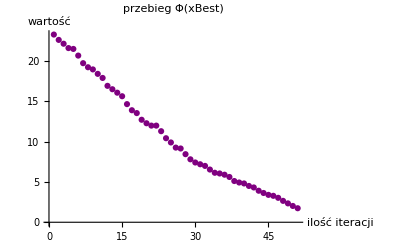
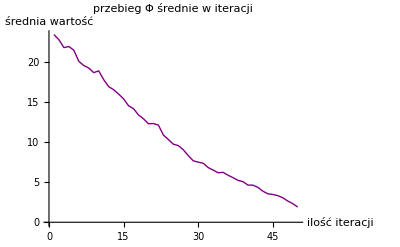
fMin(1.09955, -0.727848)=1.73877 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[Metropolis[SphericFunction2D,-5,5,-5,5,500,50,5,0.1,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

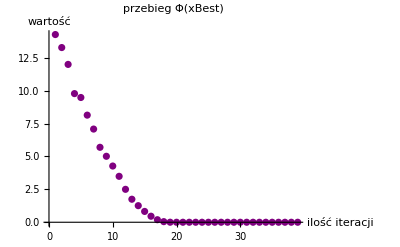
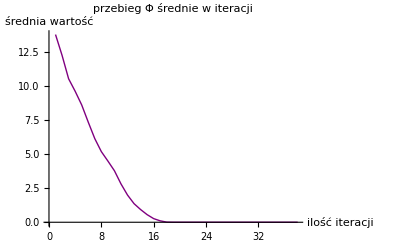
fMin(0.00638356, -0.00066967)=0.0000411983 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[symulowaneWyżarzanie[SphericFunction2D,-5,5,-5,5,50,3,5,0.1,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

-> funkcja Rastrigin’a

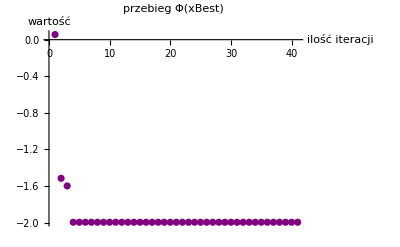
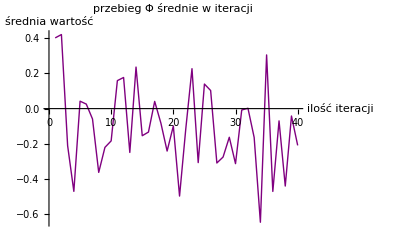
fMin(-0.00414146, -0.00302339)=-1.99572 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[Metropolis[RastriginFunction2D,-1,1,-1,1,100,40,20,0.4,{RandomReal[{-1,1}],RandomReal[{-1,1}]}]]
```

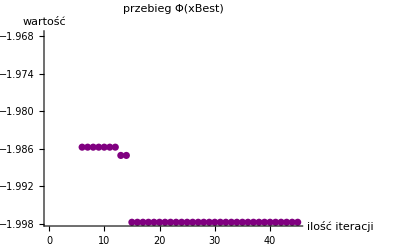
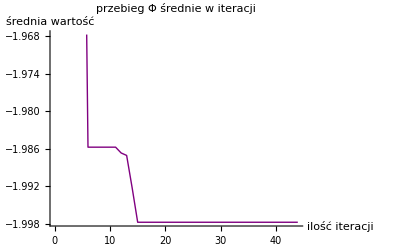
fMin(0.000259515, 0.00370903)=-1.99775 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[symulowaneWyżarzanie[RastriginFunction2D,-1,1,-1,1,100,10,20,0.3,{RandomReal[{-1,1}],RandomReal[{-1,1}]}]]
```

->  dolina Rosenbrocka

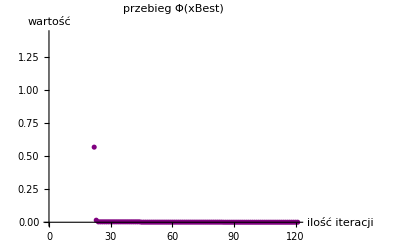
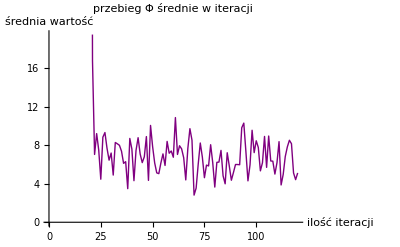
fMin(1.00284, 1.00743)=0.000308052 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[Metropolis[RosenbrockFunction2D,-5,5,-5,5,100,120,20,0.2,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

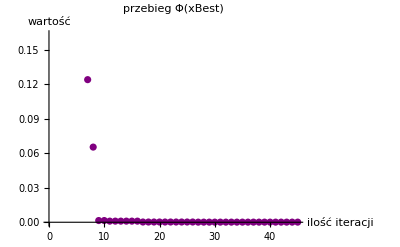
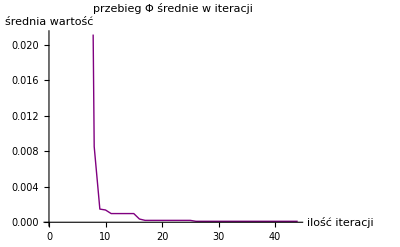
fMin(1.00857, 1.01779)=0.000107404 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[symulowaneWyżarzanie[RosenbrockFunction2D,-5,5,-5,5,100,10,20,0.2,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

Symulowane wyżarzanie radzi sobie znacznie lepiej, gdyż powtarza daną ilość razy algorytm Metropolisa, dzięki czemu nie zatrzymuje się w minimach lokalnych, tylko bez problemu znajduje globalne. Jednakże symulowane wyżarzanie jest bardziej czasochłonne. Algorytm Metropolisa też otrzymuje dobre wyniki, jeśli nie wpadnie w minimum lokalne. Wszystko również zależy od podanych parametrów.